```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A*kx/ω*Exp[k*z]-B*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A*ky/ω*Exp[k*z]-B*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A*k/ω*Exp[k*z]-I*B*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/ω-(A ⅇ^(√(kx^2+ky^2) z) kx)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/ω-(A ⅇ^(√(kx^2+ky^2) z) ky)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/ω+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))+g z

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]-g]
```

0

0

0

```mathematica
subs={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs],Simplify[(I*kx*uz[x,y,z,t]-(D[ux[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs],Simplify[(I*ky*uz[x,y,z,t]-(D[uy[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs],Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]+KroneckerDelta[k1,4]*(-1)^(n1-n2+m1-m2))*BesselI[Ω*as/2,n1-n2]*BesselI[Ω*as/2,m1-m2]-kx/ω*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[k*as/2,n1-n2]*BesselI[k*as/2,m1-m2])],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]+KroneckerDelta[k1,6]*(-1)^(n1-n2+m1-m2))*BesselI[Ω*as/2,n1-n2]*BesselI[Ω*as/2,m1-m2]-ky/ω*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[k*as/2,n1-n2]*BesselI[k*as/2,m1-m2])],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]+KroneckerDelta[k1,8]*(-1)^(n1-n2+m1-m2))*BesselI[Ω*as/2,n1-n2]*BesselI[Ω*as/2,m1-m2]-I*k/ω*(KroneckerDelta[k1,1]-KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[k*as/2,n1-n2]*BesselI[k*as/2,m1-m2])],Simplify[(-g*(h[x,y,z,t]-h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs]},{k1,1,9}]]
```

{{0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0},{0,0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,-√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0},{0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0},{0,0,0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0},{-1/(ω+l1 ωd)ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ω+l1 ωd)ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,-ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,ⅈ (ω+l1 ωd) l1,l2 m1,m2 n1,n2},{-(kx BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,((-1)^(1+m1-m2+n1-n2) kx BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,0,0,0,0,0},{-(ky BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,((-1)^(1+m1-m2+n1-n2) ky BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,0,0,BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,0,0,0},{-(ⅈ √(kx^2+ky^2) BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,(ⅈ (-1)^(m1-m2+n1-n2) √(kx^2+ky^2) BesselI[1/2 as √(kx^2+ky^2),m1-m2] BesselI[1/2 as √(kx^2+ky^2),n1-n2] l1,l2)/ω,0,0,0,0,BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),m1-m2] BesselI[1/2 as √(kx^2+ky^2+(ⅈ ρ ω)/μ),n1-n2] l1,l2,0},{-1/(ω+l1 ωd)2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ ((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,-1/(ω+l1 ωd)2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ ((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,0,0,-2 ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,2 ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,(-g-σ ((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2}}

```mathematica
eqs2=Transpose[Table[{0,0,0,0,0,0,0,0,KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (-1+l1,l2+1+l1,l2) m1,m2 n1,n2}}

```mathematica
M2=3;
M=3;
mat1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[eqs1,{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];
mat2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[eqs2,{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];
```

```mathematica
g=980;
σ=72;
q1=2*Pi*{1,0};
q2=2*Pi*{0,1};
μ=0.009;
ρ=1;

h0=1;
as=0.0;
ωd=10;
sys={mat1,mat2}/.ω->ωd/2/.qy->0/.qx->2*Pi/2;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]
```

General::munfl: Exp[-3606.88] is too small to represent as a normalized machine number; precision may be lost.

### Thin film

```mathematica
Clear[σ]
Clear[ρ]
Clear[μ]
H[x_,t_]:=H0+h*Exp[I*k*x+I*s*t]
Hs[x_]:=As*Sin[ks*x];
```

```mathematica
mat=FullSimplify[Table[Expand[TrigToExp[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]]]/.Exp[u_]:>Exp[Expand[u]]/.Exp[a_]:>0,{n,-3,3},{m,-1,1}]/.h->1]
```

{{-(ad As^3 k (k-3 ks) ρ)/(48 μ),(ⅈ As^3 k (k-3 ks) (g ρ+k^2 σ))/(24 μ),(ad As^3 k (k-3 ks) ρ)/(48 μ)},{-(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ),-(As^2 H0 k (k-2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ)},{(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ),-(ⅈ As (As^2+4 H0^2) k (k-ks) (g ρ+k^2 σ))/(8 μ),-(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ)},{(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ),ⅈ s+(H0 (3 As^2+2 H0^2) k^2 (g ρ+k^2 σ))/(6 μ),-(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ)},{-(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ),(ⅈ As (As^2+4 H0^2) k (k+ks) (g ρ+k^2 σ))/(8 μ),(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ)},{-(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ),-(As^2 H0 k (k+2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ)},{(ad As^3 k (k+3 ks) ρ)/(48 μ),-(ⅈ As^3 k (k+3 ks) (g ρ+k^2 σ))/(24 μ),-(ad As^3 k (k+3 ks) ρ)/(48 μ)}}

```mathematica
n=-2;
m=1;
AbsoluteTiming[Simplify[h*mat[[n+4,m+2]]/(Integrate[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]*Evaluate[Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]],{x,0,2*Pi/ks},{t,0,2*Pi/ωd}]/(2*Pi/ks)/(2*Pi/ωd))]]
```

{59.808,1}

```mathematica
μ=10^-3;
ρ=1;
σ=72;
g=980;
H0=0.1;
As=0.8*H0;
M2=5;
A[k_,ks_,ad_]=-ArrayFlatten[-I*Table[If[Abs[n1-n2]<=3&&Abs[m1-m2]<=1,(mat[[n1-n2+4,m1-m2+2]]/.k->k-n1*ks),0],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]/.s->0];
```

```mathematica
Dimensions[A[k,ks,ad]]
```

{121,121}

```mathematica
A[k,ks,ad]
```

{{(0.+0.653333 ⅈ) (980+72 (k-5 ks)^2) (k-5 ks)^2,(-0.326667+0. ⅈ) ad (k-5 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (980+72 (k-4 ks)^2) (k-5 ks) (k-4 ks),(0.+0.232 ⅈ) ad (k-5 ks) (k-4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (980+72 (k-3 ks)^2) (k-5 ks) (k-3 ks),(0.08+0. ⅈ) ad (k-5 ks) (k-3 ks),0,0,0,0,0,0,0,0,0,55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},119,{0,119,1}}
 |  |  |  |

```mathematica
A[k,ks,ad][[12]]
```

{(-0.464+0. ⅈ) (k+4 ks) (k+5 ks) (980+72 (k+4 ks)^2),(0.-0.232 ⅈ) ad (k+4 ks) (k+5 ks),0,0,0,0,0,0,0,0,0,(0.+0.653333 ⅈ) (k+4 ks)^2 (980+72 (k+4 ks)^2),(-0.326667+0. ⅈ) ad (k+4 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (k+3 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.+0.232 ⅈ) ad (k+3 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (k+2 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.08+0. ⅈ) ad (k+2 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(-0.0213333+0. ⅈ) (k+ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.-0.0106667 ⅈ) ad (k+ks) (k+4 ks),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

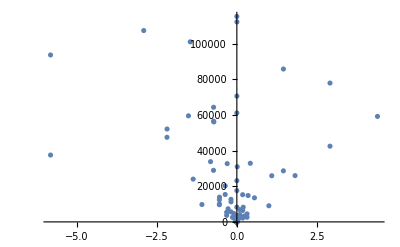

```mathematica
ListPlot[{Re[#],Im[#]}&/@Eigenvalues[A[0.5,1.0, 1000]],PlotRange->All]
```

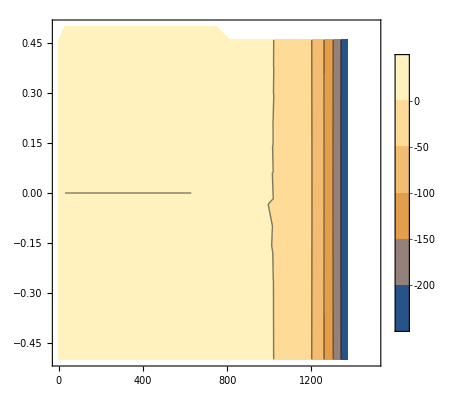

```mathematica
num=50;
Monitor[
vals=Table[{ad,k,MinimalBy[{Re[#],Im[#]}&/@Eigenvalues[A[k,1.0,ad]],#[[2]]&][[1,2]]},{ad,0,1500,1500/num},{k,-1/2,1/2,1.0/num}];,{ad,k}]
ListContourPlot[Flatten[vals,1],PlotLegends->True]
```

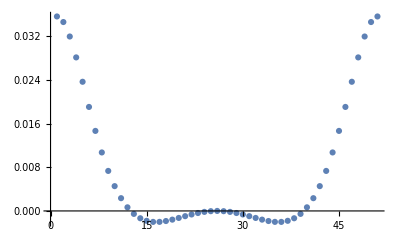

```mathematica
ListPlot[vals[[num/2+10,All,3]]]
```

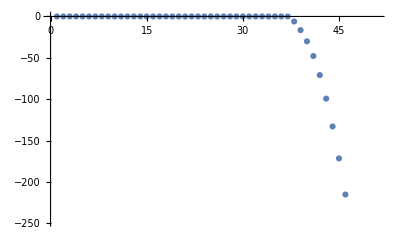

```mathematica
ListPlot[vals[[All,num/2+1,3]]]
```